```mathematica
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\nEDM\\psi-nedm\\Analysis\\mNStar"]];
Print["(DescDir) Rawdata Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\analysis-mirror_neutrons\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",ScrDir="C:\\Users\\tmpra\\Dropbox\\Scratch"];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures\\nstar"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
];
metaStructure={Real,Word,Real,Real,Real,Real,Real};
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
```

Working Directory: C:\Users\tmpra\Dropbox\nEDM\psi-nedm\Analysis\mNStar

(DescDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\analysis-mirror_neutrons\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

```mathematica
descdat=ReadList[StringJoin[descDir,"\\","desc.dat"],{Word,Word,Word,Number,Number,Number,Number,Word}];
Print["Runs in the list: ",runNum=descdat[[;;,4]]];
Print["Storage time in the list: ",ts2=descdat[[;;,7]]];
Print["#Runs in the list: ",runn=Dimensions[runNum][[1]]];
bkgcou=Table[{},{k,1,runn}];moncou=Table[0,{k,1,runn}];
moncou=Table[{},{k,1,runn}];moncou=Table[0,{k,1,runn}];
Monitor[
ptdat2=Table[Table[{0,{0,0}},{k,1,Round[(histlast2-histbeg2)/binw2]}],{l,1,runn}];
histbeg2=0*(10^9);histlast2=600*(10^9);binw2=1*(10^9);
For[runi=1,runi≤runn,runi++,
If[runi≠17,
Clear[data,histdata2];
maxCy=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[runi]],10,6],"\\",IntegerString[runNum[[runi]],10,6],"_Meta3.edm"],metaStructure2][[-1]][[2]];
bkgcou[[runi]]={};
moncou[[runi]]={};
icycle=1;
data=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[runi]],10,6],"\\",IntegerString[runNum[[runi]],10,6],"_UCNdet_",IntegerString[icycle,10,3],"_0001.fast.ascii"],metaStructure];
Print["Read Run #",runNum[[runi]]];
dimdata=Dimensions[data][[1]];
histdata2=HistogramList[data[[1;;dimdata,4]],{histbeg2,histlast2,binw2}];
For[i=1,i<=Dimensions[histdata2[[2]]][[1]],i++,
ptdat2[[runi]][[i]][[1]]=(histdata2[[1]][[i]]+((-histdata2[[1]][[1]]+histdata2[[1]][[2]])/2))/(10^9);
ptdat2[[runi]][[i]][[2]][[1]]=histdata2[[2]][[i]];
ptdat2[[runi]][[i]][[2]][[2]]=Sqrt[ptdat2[[runi]][[i]][[2]][[1]]];
];
];
];,
ProgressIndicator[runi/runn,ImageSize->{1000,100}]]
ProgressIndicator[1,ImageSize->{1000,100}]
```

Runs in the list: {12693,12695,12697,12704,12707,12770,12771,12772,12773,12774,12775,12778,12779,12780,12781,13099,13101,13102,13103,13104,13105,13106,13107,13108,13109,13110,13111,13112,13132,13133,13134,13135,13136,13137,13138,13139,13140,13141,13142,13145,13146}

Storage time in the list: {180,180,180,380,380,200,220,240,260,280,300,320,340,360,300,380,365,350,335,320,305,290,275,260,245,230,215,200,170,155,140,125,110,95,80,65,50,35,180,0,180}

#Runs in the list: 41

Read Run #12693

Read Run #12695

Read Run #12697

Read Run #12704

Read Run #12707

Read Run #12770

Read Run #12771

Read Run #12772

Read Run #12773

Read Run #12774

Read Run #12775

Read Run #12778

Read Run #12779

Read Run #12780

Read Run #12781

Read Run #13099

Read Run #13102

Read Run #13103

Read Run #13104

Read Run #13105

Read Run #13106

Read Run #13107

Read Run #13108

Read Run #13109

Read Run #13110

Read Run #13111

Read Run #13112

Read Run #13132

Read Run #13133

Read Run #13134

Read Run #13135

Read Run #13136

Read Run #13137

Read Run #13138

Read Run #13139

Read Run #13140

Read Run #13141

Read Run #13142

Read Run #13145

Read Run #13146

```mathematica
Clear[nlm,aa]
stft=10;
endft=55;
pt=Table[0,{k,1,runn}];
ptft=Table[{0,{0,0}},{k,1,runn}];
For[icycle=1,icycle≤runn,icycle++,
If[(icycle≠17&&ts2[[icycle]]≠230),
Print["Cycle # ",runNum[[icycle]],"   ",ts2[[icycle]]];
ftdat=Table[Transpose[{ptdat2[[icycle]][[;;,1]],ptdat2[[icycle]][[;;,2]][[;;,1]]}][[k]],{k,Round[30+ts2[[icycle]]+stft],Round[30+ts2[[icycle]]+stft+endft]}];
nlm=NonlinearModelFit[ftdat,{aa+(bb Exp[cc (xx-dd)])},{{aa,1},{bb,30000},{cc,-.4},{dd,33}},xx,Method->NMinimize];
fitparam={aa/.nlm[[1]][[2]],bb/.nlm[[1]][[2]],cc/.nlm[[1]][[2]],dd/.nlm[[1]][[2]]};
fitparamerr=SetPrecision[N[nlm["ParameterErrors"]],10];
pt[[icycle]]=Show[{
EDALogListPlot[ptdat2[[icycle]]+.1, PlotStyle->{Blue},Joined->True,Filling->Axis,PlotRange->{{0,600},{1,100000}},Frame->True,FrameLabel->{"Time (s)","# UCN Counts"},TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, Medium},
PlotLabel->StringJoin["t_s = ",ToString[Round[23+ts2[[icycle]]]]," s, N_EmptyingExp[",ToString[fitparam[[3]]],"(t-t_0)]"]],
EDALogListPlot[Table[{k,Abs[fitparam[[1]]+fitparam[[2]]Exp[fitparam[[3]](k-fitparam[[4]])]]},{k,Round[30+ts2[[icycle]]+stft],Round[30+ts2[[icycle]]+stft+endft]}], PlotStyle->{Red},Joined->True,Filling->Axis,PlotRange->{{0,600},{.1,40000}},Frame->True,FrameLabel->{"Time (s)","# UCN Counts"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, None}]
}];
ptft[[icycle]]={Round[23+ts2[[icycle]]],{-(1/PlusMinus[fitparam[[3]],fitparamerr[[3]]])[[1]],2(1/PlusMinus[fitparam[[3]],fitparamerr[[3]]])[[2]]}};
];
];
width=3;
exppt=GraphicsGrid[ArrayReshape[pt,{Ceiling[runn/width],width}]];
ptft2=Select[ptft,#[[2]][[2]]<1&];
```

Cycle # 12693   180

Cycle # 12695   180

Cycle # 12697   180

Cycle # 12704   380

Cycle # 12707   380

Cycle # 12770   200

Cycle # 12771   220

Cycle # 12772   240

Cycle # 12773   260

Cycle # 12774   280

Cycle # 12775   300

Cycle # 12778   320

Cycle # 12779   340

Cycle # 12780   360

Cycle # 12781   300

Cycle # 13099   380

Cycle # 13102   350

Cycle # 13103   335

Cycle # 13104   320

Cycle # 13105   305

Cycle # 13106   290

Cycle # 13107   275

Cycle # 13108   260

Cycle # 13109   245

Cycle # 13111   215

Cycle # 13112   200

Cycle # 13132   170

Cycle # 13133   155

Cycle # 13134   140

Cycle # 13135   125

Cycle # 13136   110

Cycle # 13137   95

Cycle # 13138   80

Cycle # 13139   65

Cycle # 13140   50

Cycle # 13141   35

Cycle # 13142   180

Cycle # 13145   0

Cycle # 13146   180

```mathematica
Export[StringJoin[PicDir,"\\","t_emptying2.png"],exppt]
```

C:\Users\Prajwal\Dropbox\nEDM\Pictures\nstar\t_emptying2.png

```mathematica
Show[{
EDAListPlot[ptft2,PlotRange->{{180,420},{9.1,13.9}},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],PlotStyle->{{Thickness[.005],Black}},FrameLabel->{"t_Storage^* (s)","τ_emp (s)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->38],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000},PlotLabel-> "τ_emp=(11.31±0.26) s",PlotMarkers->{Automatic,38}],
EDAListPlot[ptft2,PlotRange->{{180,420},{9.1,13.9}},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],PlotStyle->Black,FrameLabel->{"t_Storage^* (s)","τ_emp (s)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->38],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000},PlotLabel-> "τ_emp=(11.31±0.26) s"],
Plot[{11.31,11.31+0.24,11.31-0.24,11.31779-0.240741,11.31779+0.240741},{x,180,420},Filling->{2->{3}},FillingStyle->{Opacity[.5],Blue},PlotStyle->{{Blue,Thickness[.0075]},None,None,{Blue,Thickness[.0075],Dashed},{Blue,Thickness[.0075],Dashed}}]
}]
```

-Graphics-

{{203,{11.08,0.3}},{203,{11.38,0.32}},{203,{11.12,0.28}},{403,{10.82,0.42}},{403,{11.68,0.42}},{223,{11.08,0.38}},{243,{11.28,0.42}},{263,{11.2,0.36}},{283,{11.22,0.26}},{303,{11.47,0.46}},{363,{10.94,0.46}},{403,{11.09,0.48}},{373,{11.04,0.48}},{343,{11.2,0.38}},{328,{11.55,0.4}},{313,{11.56,0.42}},{298,{11.1,0.38}},{268,{11.2,0.38}},{238,{11.23,0.4}},{223,{11.07,0.34}},{193,{11.,0.34}},{178,{10.91,0.22}},{203,{11.38,0.28}},{203,{10.67,0.28}}}

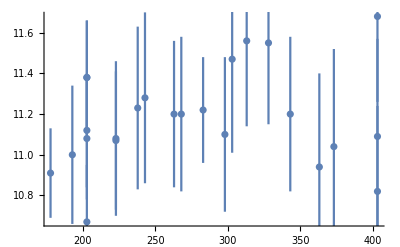

τ_emp=11.1779±0.240741

{{203,{11.08,0.3}},{203,{11.38,0.32}},{203,{11.12,0.28}},{403,{10.82,0.42}},{403,{11.68,0.42}},{223,{11.08,0.38}},{243,{11.28,0.42}},{263,{11.2,0.36}},{283,{11.22,0.26}},{303,{11.47,0.46}},{363,{10.94,0.46}},{403,{11.09,0.48}},{0,{0,0}},{373,{11.04,0.48}},{343,{11.2,0.38}},{328,{11.55,0.4}},{313,{11.56,0.42}},{298,{11.1,0.38}},{268,{11.2,0.38}},{0,{0,0}},{238,{11.23,0.4}},{223,{11.07,0.34}},{193,{11.,0.34}},{178,{10.91,0.22}},{163,{11.,0.28}},{148,{10.67,0.22}},{133,{10.78,0.24}},{118,{10.38,0.26}},{103,{10.576,0.172}},{88,{10.22,0.14}},{58,{9.79,0.24}},{203,{11.38,0.28}},{203,{10.67,0.28}}}

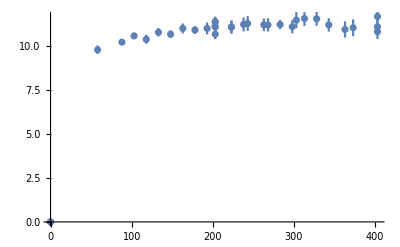

```mathematica
ptft3=Select[ptft,(#[[2]][[2]]<.5&&#[[1]]>175)&]
EDAListPlot[ptft3,PlotRange->Full]
StringJoin["τ_emp=",ToString[Mean[ptft3[[;;,2]][[;;,1]]]],"±",ToString[StandardDeviation[ptft3[[;;,2]][[;;,1]]]]]
```